```mathematica
bm
```

{{2,0.0478908,-0.0557682,-0.0900656},{4,-0.0310581,-0.00374472,-0.161852},{6,-0.0612285,-0.127748,-0.112311},{8,-0.124048,-0.103401,-0.173025},{10,-0.124711,-0.168814,-0.191312},{12,-0.219705,-0.24935,-0.11477},{14,-0.186902,-0.229631,-0.254824},{16,-0.333138,-0.222069,-0.222239}}

```mathematica
(*
nMeas=50000, nStep=30, loop=0.05*0.05;
parallel
*)
```

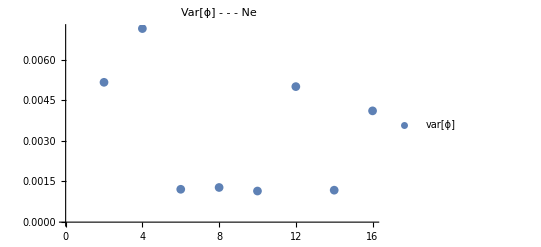

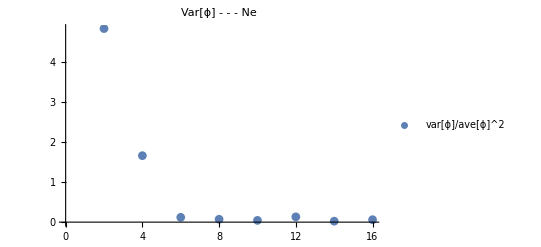

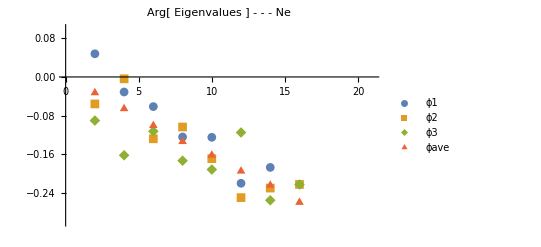

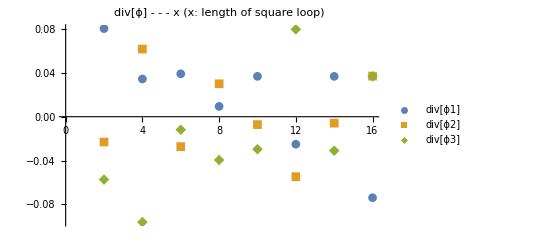

```mathematica
bm=Import["Google Drive/jie_programs/QHlattice/test_error/test_error_Ne_sl_para","Table"];
n:=Length[bm]
x=Table[bm[[i]][[1]],{i,1,n}];
phase1= Table[{x[[i]],bm[[i]][[2]]},{i,1,n}];
phase2= Table[{x[[i]],bm[[i]][[3]]},{i,1,n}];
phase3= Table[{x[[i]],bm[[i]][[4]]},{i,1,n}];
ave=Table[(bm[[i]][[2]]+bm[[i]][[3]]+bm[[i]][[4]])/3,{i,n}];
phaseave= Table[{x[[i]],ave[[i]]},{i,1,n}];
ϕ1dif= Table[{x[[i]],bm[[i]][[2]]-ave[[i]]},{i,1,n}];
ϕ2dif= Table[{x[[i]],bm[[i]][[3]]-ave[[i]]},{i,1,n}];
ϕ3dif= Table[{x[[i]],bm[[i]][[4]]-ave[[i]]},{i,1,n}];

phase=Table[Table[bm[[k]][[i]],{k,n}],{i,2,4}];
varphase=Table[{x[[i]],Variance[phase][[i]]},{i,n}];
varphase2=Table[{x[[i]],Variance[phase][[i]]/(ave[[i]])^2},{i,n}];
ListPlot[varphase,PlotLegends->{"var[ϕ]"},PlotMarkers->Automatic, PlotLabel->"Var[ϕ] - - - Ne"]
ListPlot[varphase2,PlotLegends->{"var[ϕ]/ave[ϕ]^2"},PlotMarkers->Automatic, PlotLabel->"Var[ϕ] - - - Ne"]

ListPlot[{phase1,phase2,phase3,phaseave},PlotLegends->{"ϕ1","ϕ2", "ϕ3","ϕave"},PlotMarkers->Automatic, PlotLabel->"Arg[ Eigenvalues ] - - - Ne",PlotRange->{{0,21},{-0.3,0.1}}]

ListPlot[{ϕ1dif,ϕ2dif,ϕ3dif},PlotLegends->{"div[ϕ1]","div[ϕ2]", "div[ϕ3]"},PlotMarkers->Automatic, PlotLabel->"div[ϕ] - - - x (x: length of square loop)"]
```